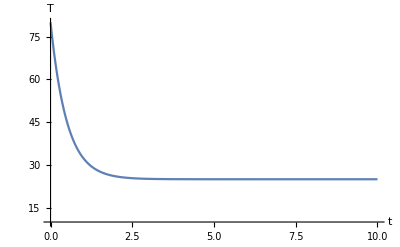

```mathematica
k := 2; 
c := 25;
t0:=80;
s0=NDSolve[{D[T[t],t]==-k*(T[t]-c), T[0] == t0},T,{t,0,10}];
Plot[Evaluate[{T[t]/.s0}], {t,0,10},PlotRange->{{0,10},{10,80}}, AxesLabel->{t,T}]
```

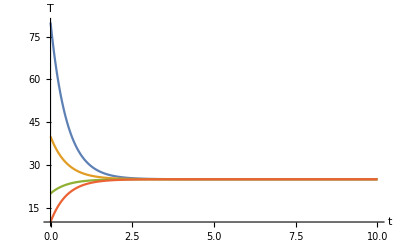

```mathematica
k := 2; 
c := 25;
s0=NDSolve[{D[T[t],t]==-k*(T[t]-c), T[0] == 80},T,{t,0,10}];
s1=NDSolve[{D[T[t],t]==-k*(T[t]-c), T[0] == 40},T,{t,0,10}];
s2=NDSolve[{D[T[t],t]==-k*(T[t]-c), T[0] == 20},T,{t,0,10}];
s3=NDSolve[{D[T[t],t]==-k*(T[t]-c), T[0] == 10},T,{t,0,10}];
img= Plot[{Evaluate[{T[t]/.s0}],Evaluate[{T[t]/.s1}],Evaluate[{T[t]/.s2}],Evaluate[{T[t]/.s3}]},{t,0,10}, PlotRange->{{0,10},{10,80}}, AxesLabel->{t,T}]
```

```mathematica
Export["~/Desktop/img.svg",img]
```

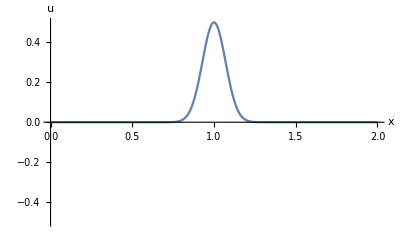

```mathematica
k:=2
img=Plot[0.5*E^(-100*((x-1)^2)),{x,0,2}, PlotRange->{{0,2},{-0.5,0.5}}, AxesLabel->{x,u}]
```

```mathematica
Export["~/Desktop/init.svg",img]
```

~/Desktop/init.svg

```mathematica
s=NDSolve[{D[u[t,x],t,t]==0.02*(D[u[t,x],x,x]),u[t,0]==0,u[t,2]==0,u[0,x]==0.5*E^(-100*((x-1)^2)),Derivative[1,0][u][0,x]==0},u,{t,0,20},{x,0,2}];
gif=Table[Plot[Evaluate[u[t,x]/. s],{x,0,2},AxesLabel->{x,u},PlotRange->{{0,2},{-0.5,0.5}}, PlotLabel->"t="<> ToString[NumberForm[t,{2,2}]]],{t,0,20,0.5}];
Export["~/Desktop/1d_new.gif",gif]
```

~/Desktop/1d_new.gif

```mathematica
img=Plot3D[0.5*E^(-100*((x-1)^2 + (y-1)^2)),{x,0,2},{y,0,2},PlotRange->{{0,2},{0,2},{-0.5,0.5}},AxesLabel->{x,y,u}]
Export["~/Desktop/init2.svg",img]
```

-Graphics3D-

~/Desktop/init2.svg

```mathematica
s=NDSolve[{D[u[t,x,y],t,t]==0.02*(D[u[t,x,y],x,x]+D[u[t,x,y],y,y]),u[t,0,y]==0,u[t,2,y]==0,u[t,x,0]==0,u[t,x,2]==0,u[0,x,y]==0.5*E^(-100*((x-1)^2+(y-1)^2)),Derivative[1,0,0][u][0,x,y]==0},u,{t,0,12},{x,0,2},{y,0,2}];
gif=Table[Plot3D[Evaluate[u[t,x,y]/. s],{x,0,2},{y,0,2},AxesLabel->{x,y,u},PlotRange->{{0,2},{0,2},{-0.5,0.5}},PlotLabel->"t="<> ToString[NumberForm[t,{2,2}]]],{t,0,12,0.5}];
Export["~/Desktop/2dWave.gif",gif]
```

~/Desktop/2dWave.gif

```mathematica
s=NDSolve[{D[u[t,x,y],t,t]==0.02*(D[u[t,x,y],x,x]+D[u[t,x,y],y,y]),u[t,0,y]==0,u[t,2,y]==0,u[t,x,0]==0,u[t,x,2]==0,u[0,x,y]==0.5*E^(-100*((x-0.5)^2+(y-0.5)^2))+0.3*E^(-100*((x-1.5)^2+(y-1.5)^2)),Derivative[1,0,0][u][0,x,y]==0},u,{t,0,12},{x,0,2},{y,0,2}];
gif=Table[Plot3D[Evaluate[u[t,x,y]/. s],{x,0,2},{y,0,2},AxesLabel->{x,y,u},PlotRange->{{0,2},{0,2},{-0.5,0.5}},PlotLabel->"t="<> ToString[NumberForm[t,{2,2}]]],{t,0,12,0.5}];
Export["~/Desktop/Cool2dWave.gif",gif]
```

~/Desktop/Cool2dWave.gif

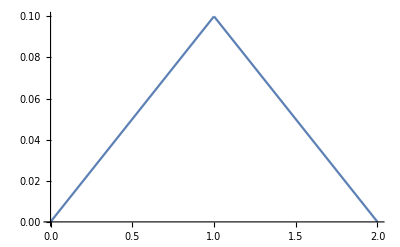

```mathematica
Plot[Piecewise[{{0.1*x,x<1},{-0.1*x + 0.2,x>1}}],{x,0,2}]
```

```mathematica
s5=NDSolve[{D[u[t,x],t,t]==0.5*(D[u[t,x],x,x]),u[t,0]==0,u[t,2]==0,u[0,x]== Piecewise[{{0.1*x,x<1},{-0.1*x + 0.2,x>1}}],Derivative[1,0][u][0,x]==0},u,{t,0,12},{x,0,2}, Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MaxPoints"->101}}]
```

NDSolve::mxsst: Using maximum number of grid points 101 allowed by the MaxPoints or MinStepSize options for independent variable x.

NDSolve::eerr: Warning: scaled local spatial error estimate of 554.746 at t = 12. in the direction of independent variable x is much greater than the prescribed error tolerance. Grid spacing with 101 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

{{u→InterpolatingFunction[{{0., 12.}, {0., 2.}}, <>]}}

```mathematica
gif=Table[Plot[Evaluate[u[t,x]/. s5],{x,0,2},AxesLabel->Automatic,PlotRange->{{0,2},{-0.5,0.5}}],{t,0,12,0.5}];
```

```mathematica
Export["~/Desktop/guitar.gif",gif]
```

~/Desktop/guitar.gif